-Graphics3D-

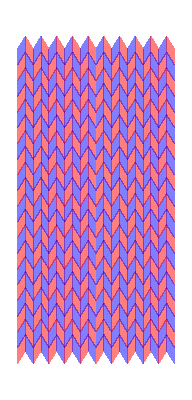

{}

```mathematica
(*Import and flatten data*)
y=Import["y.csv","CSV"]//Flatten;
yO=Import["yOpt.csv","CSV"]//Flatten;
x=Import["x.csv","CSV"]//Flatten;
xO=Import["xOpt.csv","CSV"]//Flatten;

(*Split into 9 pairs*)
yN=Partition[y,3];
yOpt=Partition[yO,3];
xN=Partition[x,2];
xOpt=Partition[xO,2];

(*Define panels indices*)
indexLists={{1,2,5,6},{5,6,7,8},{4,5,8,9},{2,3,4,5}};

yl1=yN[[7]]-yN[[1]];
yl2=yN[[3]]-yN[[1]];

polygonsY={}; (*Initialize an empty list*)

(*Number of repetitions along each lattice direction*)
n=10; (*Adjust for desired tiling range*)

For[j=1,j<=n,j++,For[i=1,i<=n,i++,translation=i*yl1+j*yl2;
For[l=1,l<=Length[indexLists],l++,AppendTo[polygonsY,{Opacity[0.65],If[Mod[l,2]==0,Blue,Red],Polygon[#+translation&/@yOpt[[indexLists[[l]]]]]}]];];];

(*Display the 3D graphics*)
Graphics3D[polygonsY]

polygonsX={};

xl1=xN[[7]]-xN[[1]];
xl2=xN[[3]]-xN[[1]];

For[j=1,j<=n,j++,
For[i=1,i<=n,i++,translation=i*xl1+j*xl2;
For[l=1,l<=Length[indexLists],l++,AppendTo[polygonsX,{Opacity[0.5],If[Mod[l,2]==0,Blue,Red],Polygon[#+translation&/@xOpt[[indexLists[[l]]]]]}]];];];

(*Display the 3D graphics*)
Graphics[polygonsX]
```